```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY182_cloudy/sec_int_data/412nm.dat"]
```

{{1.83648,-0.283876},{1.67469,-0.189467},{1.55096,-0.164474},{1.77833,-0.234521},{1.08395,0.116983},{1.0884,1.4856},{1.10777,0.0233258},{1.1184,0.0630687},{1.90886,-0.31744}}

1.49731-0.986975 x

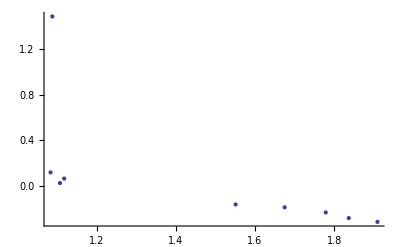

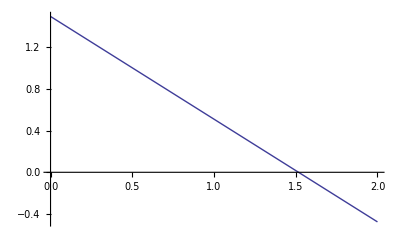

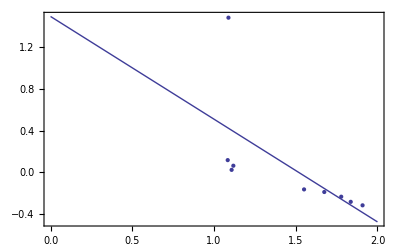

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```